```mathematica
List1=List[0.10592396885742734,0.07387709757437771,0.05109731699884372,0.01191113503663902,0.023928688144272018,0.016225709318418175,0.010944387038254979,0.0073468294784134235,0.004910407173174931,0.003268947182407089,0.0021682761371529004,0.0014333883172937744,0.000944642527302181,0.0006207616710087517,0.0004068411296780474,0.00026597878798647603,0.0001734854444473261,0.00011291138911692114,0.00007333813244529609,0.00004754367277856014,0.000030766287416396614,0.00001987565608235858,0.00001281954761161731,5.813430588265238*^-7,5.309294783949123*^-6,3.4097005328784832*^-6,2.1869256577527865*^-6,1.400933614042318*^-6,8.963802170820611*^-7]
```

{0.105924,0.0738771,0.0510973,0.0119111,0.0239287,0.0162257,0.0109444,0.00734683,0.00491041,0.00326895,0.00216828,0.00143339,0.000944643,0.000620762,0.000406841,0.000265979,0.000173485,0.000112911,0.0000733381,0.0000475437,0.0000307663,0.0000198757,0.0000128195,5.81343×10^-7,5.30929×10^-6,3.4097×10^-6,2.18693×10^-6,1.40093×10^-6,8.9638×10^-7}

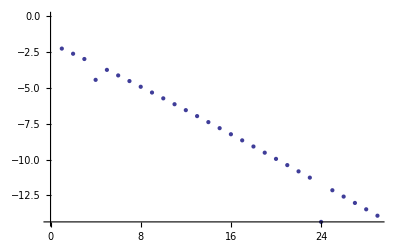

```mathematica
ListPlot[Log[List1]]
```

```mathematica
FindFit[Log[List1],a*x+b,{a,b},x]
```

{a→-0.425599,b→-1.6463}

```mathematica
List2=List[0.00026597878798647603,0.0001734854444473261,0.00011291138911692114,0.00007333813244529609,0.00004754367277856014,0.000030766287416396614,0.00001987565608235858,0.00001281954761161731,5.813430588265238*^-7,5.309294783949123*^-6,3.4097005328784832*^-6,2.1869256577527865*^-6,1.400933614042318*^-6,8.963802170820611*^-7]
```

{0.000265979,0.000173485,0.000112911,0.0000733381,0.0000475437,0.0000307663,0.0000198757,0.0000128195,5.81343×10^-7,5.30929×10^-6,3.4097×10^-6,2.18693×10^-6,1.40093×10^-6,8.9638×10^-7}

```mathematica
FindFit[Log[List2],a*x+b,{a,b},x]
```

{a→-0.455598,b→-7.83041}

```mathematica
List3=List[0.000030766287416396614,0.00001987565608235858,0.00001281954761161731,5.813430588265238*^-7,5.309294783949123*^-6,3.4097005328784832*^-6,2.1869256577527865*^-6,1.400933614042318*^-6,8.963802170820611*^-7]
```

{0.0000307663,0.0000198757,0.0000128195,5.81343×10^-7,5.30929×10^-6,3.4097×10^-6,2.18693×10^-6,1.40093×10^-6,8.9638×10^-7}

```mathematica
FindFit[Log[List3],a*x+b,{a,b},x]
```

{a→-0.397804,b→-10.4564}